```mathematica
allGraphs4[300,"parents"]
```

{243,246,54,54,3}

```mathematica
Table[allGraphs4[k,"colofourrealnull"]->Length[allGraphs4[k,"colofour"]],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→15,n12x3x4→5,n123x4→2,n1234→0,n124x3→2,n12x34→2,n13x2x4→5,n134x2→2,n13x24→2,n14x2x3→5,n14x23→2,n1x23x4→5,n1x234→2,n1x24x3→5,n1x2x34→5}

```mathematica
TableForm[Table[allGraphs4[k,"colofourrealnull"]->allGraphs4[k,"colofour"],{k,allGraphs4NullAtomKeys}]]
```

n1x2x3x4→v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4
n12x3x4→v1234+v123x4+v124x3+v12x34+v12x3x4
n123x4→v1234+v123x4
n1234→v1234
n124x3→v1234+v124x3
n12x34→v1234+v12x34
n13x2x4→v1234+v123x4+v134x2+v13x24+v13x2x4
n134x2→v1234+v134x2
n13x24→v1234+v13x24
n14x2x3→v1234+v124x3+v134x2+v14x23+v14x2x3
n14x23→v1234+v14x23
n1x23x4→v1234+v123x4+v14x23+v1x234+v1x23x4
n1x234→v1234+v1x234
n1x24x3→v1234+v124x3+v13x24+v1x234+v1x24x3
n1x2x34→v1234+v12x34+v134x2+v1x234+v1x2x34

```mathematica
TableForm[Sort[Table[{Length[ListofVars[ allGraphs5[k,"colofour"]]],allGraphs5[k,"colofourrealnull"]},{k,allGraphs5NullAtomKeys}]]]
```

1 | n12345
2 | n1234x5
2 | n1235x4
2 | n123x45
2 | n1245x3
2 | n124x35
2 | n125x34
2 | n12x345
2 | n1345x2
2 | n134x25
2 | n135x24
2 | n13x245
2 | n145x23
2 | n14x235
2 | n15x234
2 | n1x2345
5 | n123x4x5
5 | n124x3x5
5 | n125x3x4
5 | n12x34x5
5 | n12x35x4
5 | n12x3x45
5 | n134x2x5
5 | n135x2x4
5 | n13x24x5
5 | n13x25x4
5 | n13x2x45
5 | n145x2x3
5 | n14x23x5
5 | n14x25x3
5 | n14x2x35
5 | n15x23x4
5 | n15x24x3
5 | n15x2x34
5 | n1x234x5
5 | n1x235x4
5 | n1x23x45
5 | n1x245x3
5 | n1x24x35
5 | n1x25x34
5 | n1x2x345
15 | n12x3x4x5
15 | n13x2x4x5
15 | n14x2x3x5
15 | n15x2x3x4
15 | n1x23x4x5
15 | n1x24x3x5
15 | n1x25x3x4
15 | n1x2x34x5
15 | n1x2x35x4
15 | n1x2x3x45
52 | n1x2x3x4x5

```mathematica
TableForm[Sort[Table[{Length[ListofVars[ allGraphs6[k,"colofour"]]],allGraphs6[k,"colofourrealnull"]},{k,allGraphs6NullAtomKeys}]]]
```

1 | n123456
2 | n12345x6
2 | n12346x5
2 | n1234x56
2 | n12356x4
2 | n1235x46
2 | n1236x45
2 | n123x456
2 | n12456x3
2 | n1245x36
2 | n1246x35
2 | n124x356
2 | n1256x34
2 | n125x346
2 | n126x345
2 | n12x3456
2 | n13456x2
2 | n1345x26
2 | n1346x25
2 | n134x256
2 | n1356x24
2 | n135x246
2 | n136x245
2 | n13x2456
2 | n1456x23
2 | n145x236
2 | n146x235
2 | n14x2356
2 | n156x234
2 | n15x2346
2 | n16x2345
2 | n1x23456
5 | n1234x5x6
5 | n1235x4x6
5 | n1236x4x5
5 | n123x45x6
5 | n123x46x5
5 | n123x4x56
5 | n1245x3x6
5 | n1246x3x5
5 | n124x35x6
5 | n124x36x5
5 | n124x3x56
5 | n1256x3x4
5 | n125x34x6
5 | n125x36x4
5 | n125x3x46
5 | n126x34x5
5 | n126x35x4
5 | n126x3x45
5 | n12x345x6
5 | n12x346x5
5 | n12x34x56
5 | n12x356x4
5 | n12x35x46
5 | n12x36x45
5 | n12x3x456
5 | n1345x2x6
5 | n1346x2x5
5 | n134x25x6
5 | n134x26x5
5 | n134x2x56
5 | n1356x2x4
5 | n135x24x6
5 | n135x26x4
5 | n135x2x46
5 | n136x24x5
5 | n136x25x4
5 | n136x2x45
5 | n13x245x6
5 | n13x246x5
5 | n13x24x56
5 | n13x256x4
5 | n13x25x46
5 | n13x26x45
5 | n13x2x456
5 | n1456x2x3
5 | n145x23x6
5 | n145x26x3
5 | n145x2x36
5 | n146x23x5
5 | n146x25x3
5 | n146x2x35
5 | n14x235x6
5 | n14x236x5
5 | n14x23x56
5 | n14x256x3
5 | n14x25x36
5 | n14x26x35
5 | n14x2x356
5 | n156x23x4
5 | n156x24x3
5 | n156x2x34
5 | n15x234x6
5 | n15x236x4
5 | n15x23x46
5 | n15x246x3
5 | n15x24x36
5 | n15x26x34
5 | n15x2x346
5 | n16x234x5
5 | n16x235x4
5 | n16x23x45
5 | n16x245x3
5 | n16x24x35
5 | n16x25x34
5 | n16x2x345
5 | n1x2345x6
5 | n1x2346x5
5 | n1x234x56
5 | n1x2356x4
5 | n1x235x46
5 | n1x236x45
5 | n1x23x456
5 | n1x2456x3
5 | n1x245x36
5 | n1x246x35
5 | n1x24x356
5 | n1x256x34
5 | n1x25x346
5 | n1x26x345
5 | n1x2x3456
15 | n123x4x5x6
15 | n124x3x5x6
15 | n125x3x4x6
15 | n126x3x4x5
15 | n12x34x5x6
15 | n12x35x4x6
15 | n12x36x4x5
15 | n12x3x45x6
15 | n12x3x46x5
15 | n12x3x4x56
15 | n134x2x5x6
15 | n135x2x4x6
15 | n136x2x4x5
15 | n13x24x5x6
15 | n13x25x4x6
15 | n13x26x4x5
15 | n13x2x45x6
15 | n13x2x46x5
15 | n13x2x4x56
15 | n145x2x3x6
15 | n146x2x3x5
15 | n14x23x5x6
15 | n14x25x3x6
15 | n14x26x3x5
15 | n14x2x35x6
15 | n14x2x36x5
15 | n14x2x3x56
15 | n156x2x3x4
15 | n15x23x4x6
15 | n15x24x3x6
15 | n15x26x3x4
15 | n15x2x34x6
15 | n15x2x36x4
15 | n15x2x3x46
15 | n16x23x4x5
15 | n16x24x3x5
15 | n16x25x3x4
15 | n16x2x34x5
15 | n16x2x35x4
15 | n16x2x3x45
15 | n1x234x5x6
15 | n1x235x4x6
15 | n1x236x4x5
15 | n1x23x45x6
15 | n1x23x46x5
15 | n1x23x4x56
15 | n1x245x3x6
15 | n1x246x3x5
15 | n1x24x35x6
15 | n1x24x36x5
15 | n1x24x3x56
15 | n1x256x3x4
15 | n1x25x34x6
15 | n1x25x36x4
15 | n1x25x3x46
15 | n1x26x34x5
15 | n1x26x35x4
15 | n1x26x3x45
15 | n1x2x345x6
15 | n1x2x346x5
15 | n1x2x34x56
15 | n1x2x356x4
15 | n1x2x35x46
15 | n1x2x36x45
15 | n1x2x3x456
52 | n12x3x4x5x6
52 | n13x2x4x5x6
52 | n14x2x3x5x6
52 | n15x2x3x4x6
52 | n16x2x3x4x5
52 | n1x23x4x5x6
52 | n1x24x3x5x6
52 | n1x25x3x4x6
52 | n1x26x3x4x5
52 | n1x2x34x5x6
52 | n1x2x35x4x6
52 | n1x2x36x4x5
52 | n1x2x3x45x6
52 | n1x2x3x46x5
52 | n1x2x3x4x56
203 | n1x2x3x4x5x6

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&]
```

{360,354,352,336,334,328,282,280,274,256,120,118,112,94,40}

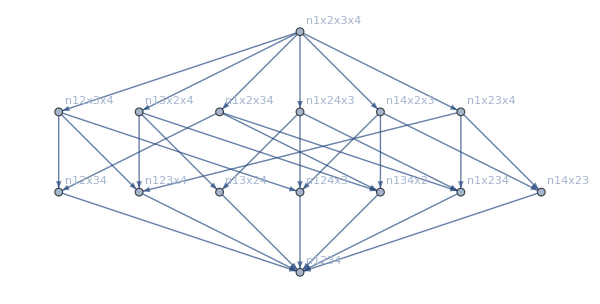
-Graphics-→-3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
-Graphics-280-3 x+6 x^2-4 x^3+x^41→0
2→2
3→18
4→84
5→260
6→630
7→1302
-Graphics-→-4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
-Graphics-361-4 x+8 x^2-5 x^3+x^41→0
2→0
3→6
4→48
5→180
6→480
7→1050
-Graphics-→n1x2345-n1x234x5-n1x245x3+n1x24x3x5
-Graphics-442x-2 x^2+x^31→0
2→2
3→12
4→36
5→80
6→150
7→252
-Graphics-→-4 n1x2345+n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5
-Graphics-283-4 x+8 x^2-5 x^3+x^41→0
2→0
3→6
4→48
5→180
6→480
7→1050
-Graphics-→n1x2345-n1x235x4-n1x2x345+n1x2x35x4
-Graphics-286x-2 x^2+x^31→0
2→2
3→12
4→36
5→80
6→150
7→252

```mathematica
TableForm[With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
Framed[
allGraphs4[k,"graph"]->
With[{sub2=MobiusGraph4[k,allGraphs4]},
Column[{
allGraphs5[k,"colofourrealnull"],

Labeled[
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->600, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
,{k,ChromaticPolynomial[allGraphs4[k,"graph"],x],Column[Table[n->ChromaticPolynomial[allGraphs4[k,"graph"],n],{n,1,7}]]},{Top,Bottom,Left}
]
}
]
]
]
,{k,Flatten[Join[{280},allGraphs4[280,"children"]]]}]
]]
```

```mathematica
TableForm[With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
Framed[
allGraphs4[k,"graph"]->
With[{sub2=MobiusGraph4[k,allGraphs4]},
Column[{
allGraphs5[k,"colofourrealnull"],

Labeled[
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->600, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
,{k,ChromaticPolynomial[allGraphs4[k,"graph"],x],Column[Table[n->ChromaticPolynomial[allGraphs4[k,"graph"],n],{n,1,7}]]},{Top,Bottom,Left}
]
}
]
]
]
,{k,Flatten[Join[{336},allGraphs4[336,"children"]]]}]
]]
```

-Graphics-→-2 n1x2345+2 n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5
-Graphics-336-2 x+5 x^2-4 x^3+x^41→0
2→0
3→12
4→72
5→240
6→600
7→1260
-Graphics-→-4 n1x2345+2 n1x234x5+2 n1x235x4-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5
-Graphics-363-4 x+8 x^2-5 x^3+x^41→0
2→0
3→6
4→48
5→180
6→480
7→1050
-Graphics-→2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4
-Graphics-3912 x-3 x^2+x^31→0
2→0
3→6
4→24
5→60
6→120
7→210
-Graphics-→-4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5
-Graphics-337-4 x+8 x^2-5 x^3+x^41→0
2→0
3→6
4→48
5→180
6→480
7→1050
-Graphics-→2 n1x2345-n1x23x45-n1x245x3-n1x2x345+n1x2x3x45
-Graphics-3652 x-3 x^2+x^31→0
2→0
3→6
4→24
5→60
6→120
7→210